# f.figure.rencon2.strange.baryons-all.single-if.ci-1.5.nb

```mathematica
NotebookFileName[]
```

C:\octet.formfactor\f.figure.rencon2.strange.baryons-all.single-if.ci-1.5.nb

this nb is to record the all baryon octets ge gm experiment data and calculated data.

extract the Line data, and build the band

## note

增加曲线透明度选项，这样可以隐藏曲线

## initial

ge`charge: octet: 1 3 4 6, line, dash, dot, dot-dash

ge`neutral: octet: 2 5 7 8, line, dash, dot, dot-dash

** ** ** ** ** ** ** ** ** ** ** **

gm/μm`charge: octet: 1 3 4 6, line, dash, dot, dot-dash

gm/μm`neutral: octet: 2 5 7 8, line, dash, dot, dot-dash

```mathematica
directory`fig=FileNameJoin[{NotebookDirectory[],"/expression-fig/"}]
```

C:\octet.formfactor\expression-fig

## global setting

选定用来绘图的数据配置

```mathematica
fontsize`frame=8;
imagesize=Scaled[.6];
```

## data initial

## import origin figs

{Λ, ci}→

{0.8,1.0} l1c1,{0.9,1.0} l2c1,{1.0,1.0} l3c1,

{0.8,1.5} l1c2,{0.9,1.5} l2c2,{1.0,1.5} l3c2

```mathematica
fig`calc`baryons`ge`total`origin=
(
(Get[
FileNameJoin[{directory`fig,
#1
}
]
])&/@
{
(*+++++++++++++++++++++++++*)
"fig.separate.baryons.ge.tot.L-0.90.ci-1.5.m"
}
);
```

```mathematica
fig`calc`baryons`gm`total`origin=(
(Get[
FileNameJoin[{directory`fig,
#1
}
]
])&/@
{
(*+++++++++++++++++++++++++*)
"fig.separate.baryons.gm.tot.L-0.90.ci-1.5.m"
}
);
```

```mathematica
fig`calc`baryons`ge`total`origin//Dimensions
fig`calc`baryons`gm`total`origin//Dimensions
```

## extract data

```mathematica
{data`f1[x_],data`f1[y_]}^:=data`f2[Join[x,y]]
```

```mathematica
{data`f1[x_]}^:=data`f2[x]
```

将Line中出现的数据用data`f1做tag，并且通过赋上值的方式合并到data`f2

f 是format的意思

fig`calc`baryons`ge`total`origin,{config,io,if,treeloop},{6,8,11,2}

```mathematica
fun`data`extract[fig`calc`baryons`ge`total`origin_]:=Table[
Cases[
fig`calc`baryons`ge`total`origin⟦config,io,if,treeloop⟧
,Line[x_]:>data`f1[x],10(*level*)
]
,{config,1,1,1}
,{io,1,8,1}
,{if,1,11,1}
,{treeloop,1,2,1}
]
```

```mathematica
data`calc`baryons`ge`total=fun`data`extract[fig`calc`baryons`ge`total`origin];
```

```mathematica
data`calc`baryons`gm`total=fun`data`extract[fig`calc`baryons`gm`total`origin];
```

```mathematica
data`calc`baryons`ge`total//Dimensions
data`calc`baryons`gm`total//Dimensions
```

## regularize data

```mathematica
{data`rearrange`ge,data`rearrange`gm}=(Transpose[
#1,
{1,2,3,4}
]&)/@{
data`calc`baryons`ge`total,data`calc`baryons`gm`total
};
```

```mathematica
data`rearrange`ge//Dimensions
data`rearrange`gm//Dimensions
```

## draw

## color initial

给定线型方案, Dashing[{}] 指定线为实线

style`line`type={Dashing[{}],Dashing[{}],Dashing[{}],Dashing[Medium],Dotted,DotDashed};

默认的曲线间填充透明度

```mathematica
filling`opacity=Opacity[0];
```

默认线宽

```mathematica
style`line`thick=Thickness[Medium];
```

线型,Dashing[{}]指定线为实线

```mathematica
style`line`type={
(*1*)Dashing[{}],
(*2*)Dashing[Medium],
(*3*)Dashing[Medium],
(*4*)Dotted,
(*5*)Dotted,
(*6*)Dashing[{}],
(*7*)Dashing[Medium],
(*8*)Dashing[Medium],
(*9*)Dashing[Medium],
(*10*)Dotted,
(*11*)Dotted
};
```

给定颜色方案，

```mathematica
style`exp={
AbsoluteThickness[_]-> AbsoluteThickness[.8],
PointSize[_]->PointSize[0.02]
};
```

```mathematica
color`default = RGBColor[0.368417, 0.506779, 0.709798];
```

1,3,4,6;2,5,7,8

```mathematica
color`array={Red,Green,Blue,Black,Cyan,Magenta,Yellow};
```

```mathematica
style`colors`theme=Array[#&,11]
style`colors`theme⟦type⟧=color`array⟦Span[1,Length[type={1,6}]]⟧;
style`colors`theme⟦type⟧=color`array⟦Span[1,Length[type={2,3,7,8,9}]]⟧;
style`colors`theme⟦type⟧=color`array⟦Span[1,Length[type={4,5,10,11}]]⟧;
```

{1,2,3,4,5,6,7,8,9,10,11}

设定11幅图的曲线style

```mathematica
style`line=Table[
Directive[
style`line`thick,style`line`type⟦if⟧,style`colors`theme⟦if⟧,Opacity[1](*opacity of the curves*)
]
,{if,1,11,1}
];
```

设置填充颜色和透明度

```mathematica
style`filling=Table[
{
1->{{2},Directive[filling`opacity,style`colors`theme⟦if⟧]},
3->{{2},Directive[filling`opacity,style`colors`theme⟦if⟧]}
}
,{if,1,11,1}
];
```

设置图例样式

```mathematica
style`legend=style`line;
```

设置框架样式

```mathematica
style`frame={
{
Directive[AbsoluteThickness[0.8],FontSize->fontsize`frame,Black],
Directive[AbsoluteThickness[0.8],FontSize->fontsize`frame,Black]
},
{
Directive[AbsoluteThickness[0.8],FontSize->fontsize`frame,Black],
Directive[AbsoluteThickness[0.8],FontSize->fontsize`frame,Black]
}
};
```

## functions to draw

data`rearrange`ge,{config,io,if,treeloop},{1,8,11,2}

data`rearrange`gm,{config,io,if,treeloop},{1,8,11,2}

**********************************

此函数产生带状图

```mathematica
fig`baryons`band[
data`rearrange_(*the fig data extracted*),config`io`if`treeloop__
]:=ListLinePlot[
data`rearrange⟦config`io`if`treeloop⟧/.{data`f2->Sequence},
PlotStyle->style`line⟦if⟧,
(*Filling->style`filling⟦range`if⟧,*)
PlotRange->All
];
```

ge`charge: octet: 1 3 4 6, line, Dashing, Dotted, DotDashed

fig`calc`baryons`ge`total⟦octet,tree-loop-total⟧

横纵轴线标记

```mathematica
framelabel`ge={
{Style["G_E^B(Q^2)",FontFamily->"Times New Roman",FontSize->fontsize`frame],None},
{Style["Q^2(GeV^2)",FontFamily->"Times New Roman",FontSize->fontsize`frame],None}
};
```

```mathematica
framelabel`gm={
{Style["G_M^B(Q^2)",FontFamily->"Times New Roman",FontSize->fontsize`frame],None},
{Style["Q^2(GeV^2)",FontFamily->"Times New Roman",FontSize->fontsize`frame],None}
};
```

对图形的细节进行调整

```mathematica
fun`fig`gegm`cn[
fig`baryons`band_,(*function, generate band figure using data of ge or gm *)
framelabel_,(*framelabel of ge or gm*)
legend`text_,(*legend text*)
legend`ps_:legend`position(*legend position*)
]:=Legended[
Show[
(fig`baryons`band/.data`f2->Sequence),
ImageSize->Large,
PlotRange->All,
PlotRangePadding->{{0,0},{Scaled[0.09],Scaled[0.09]}},
Frame->True,
FrameStyle->style`frame,
FrameLabel->framelabel
],
(*++++++++++++++++++++++++++++++*)
Placed[
Style[
LineLegend[style`legend,
(Style[#1,FontFamily->"Times New Roman",FontSize->12]&)/@legend`text
(*,LegendFunction->Framed*)
],
Magnification->fig`legend`magni
],
legend`ps
]
];
```

## fun apply

### ge

data`rearrange`ge,{1,8,11,2},{config,io,if,treeloop}

legend text and legend position

```mathematica
legend`t1=Table[i,{i,1,11,1}];
legend`ps1={
{0.8,0.6},
{0.,0.}
};
fig`legend`magni=1(*0.5*);
(*+++++++++++++++++++++++++*)
config=1;io=5;if=Span[1,11];treeloop=2;
(*+++++++++++++++++++++++++*)
fig`each`baryons`ge=Table[
fun`fig`gegm`cn[
fig`baryons`band[data`rearrange`ge,config,io,if,treeloop],
framelabel`ge,
legend`t1,
legend`ps1
]
,{io,1,8,1}
];
```

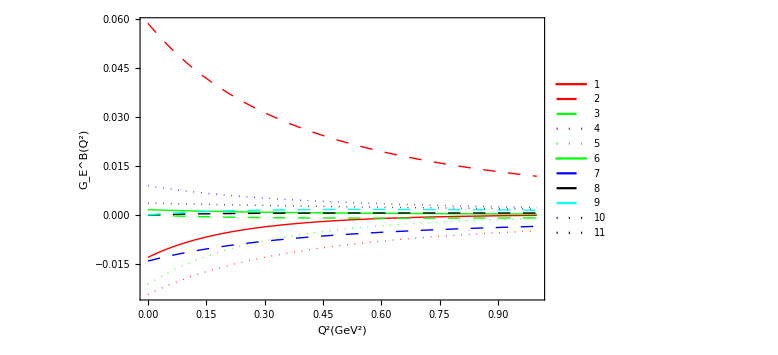

```mathematica
io=8;
fig`each`baryons`ge⟦io⟧
```

### gm

gm`charge: octet: 1 3 4 6, line, Dashing, Dotted, DotDashed

legend`t1={"Σ^-","Σ^+","p","Ξ^-"};

```mathematica
legend`t1=Table[i,{i,1,11,1}];
legend`ps1={
{0.8,0.3},
{0.,0.}
};
fig`legend`magni=1;
(*+++++++++++++++++++++++++*)
config=1;io=5;if=Span[1,11];treeloop=2;
(*+++++++++++++++++++++++++*)
fig`each`baryons`gm=Table[
fun`fig`gegm`cn[
fig`baryons`band[data`rearrange`gm,config,io,if,treeloop],
framelabel`ge,
legend`t1,
legend`ps1
]
,{io,1,8,1}
];
```

## export

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[],"/expression-results/"}]]
```

C:\octet.formfactor\expression-results

```mathematica
Export["fig`each`baryons`ge.ci-1.5.pdf",fig`each`baryons`ge//TableForm];
Export["fig`each`baryons`gm.ci-1.5.pdf",fig`each`baryons`gm//TableForm];
```